```mathematica
(** γ parameters that we will graph **)
a=0.0304482;
b=0.0515014;
c=0.0725546;
d=0.0936078;
e=0.114661;
ff=0.135714;
g=0.156767;
h=0.177821;
i=0.198874;
max=0.201137;
min=9.395*10^-3;

(** The first resonance center frequancy for the LCR circuit[kHz] **)
f0 = 6.103;
```

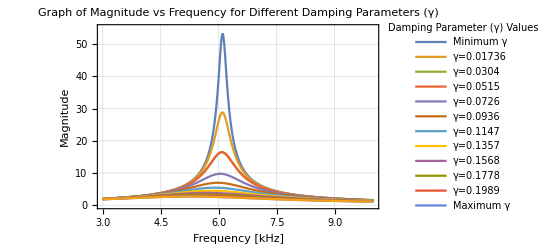

```mathematica
m[f_,γ_]:=1/(√((1-(f/f0))^2+(2γ*f/f0)^2));
plotγmin =m[f,min];
plotγ0 =m[f,aa];
plotγ1 =m[f,a];
plotγ2 =m[f,b];
plotγ3 =m[f,c];
plotγ4 =m[f,d];
plotγ5 =m[f,e];
plotγ6 =m[f,ff];
plotγ7 =m[f,g];
plotγ8 =m[f,h];
plotγ9 =m[f,i];
plotγmax =m[f,max];
Plot[{plotγmin,plotγ0,plotγ1,plotγ1,plotγ2,plotγ3,plotγ4,plotγ5,plotγ6,plotγ7,plotγ8,plotγ9,plotγmax},{f,3,10},PlotRange->{0,55},FrameLabel->{Style["Frequency [kHz]",FontSize->15],Style["Magnitude",FontSize->15]},PlotLegends->LineLegend[{"Minimum γ","γ=0.01736","γ=0.0304","γ=0.0515","γ=0.0726","γ=0.0936","γ=0.1147","γ=0.1357","γ=0.1568","γ=0.1778","γ=0.1989","Maximum γ"},LegendLabel->"Damping Parameter\n        (γ) Values",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],PlotTheme->"Detailed",PlotLabel->Style["Graph of Magnitude vs Frequency\nfor Different Damping Parameters (γ)",FontSize->18]]
```

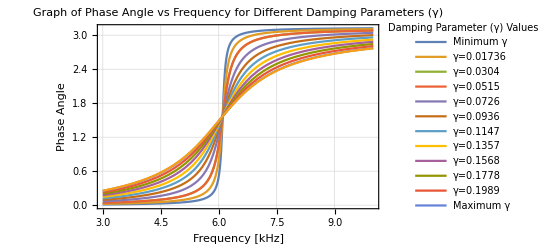

```mathematica
ϕ[f_,γ_]:=ArcCos[(1-(f^2/f0^2))/(√((1-(f/f0)^2)^2+(2γ*f/f0)^2))];
plotγmin =ϕ[f,min];
plotγ0 =ϕ[f,aa];
plotγ1 =ϕ[f,a];
plotγ2 =ϕ[f,b];
plotγ3 =ϕ[f,c];
plotγ4 =ϕ[f,d];
plotγ5 =ϕ[f,e];
plotγ6 =ϕ[f,ff];
plotγ7 =ϕ[f,g];
plotγ8 =ϕ[f,h];
plotγ9 =ϕ[f,i];
plotγmax =ϕ[f,max];
Plot[{plotγmin,plotγ0,plotγ1,plotγ1,plotγ2,plotγ3,plotγ4,plotγ5,plotγ6,plotγ7,plotγ8,plotγ9,plotγmax},{f,3,10},PlotRange->Automatic,FrameLabel->{Style["Frequency [kHz]",FontSize->15],Style["Phase Angle",FontSize->15]},PlotLegends->LineLegend[{"Minimum γ","γ=0.01736","γ=0.0304","γ=0.0515","γ=0.0726","γ=0.0936","γ=0.1147","γ=0.1357","γ=0.1568","γ=0.1778","γ=0.1989","Maximum γ"},LegendLabel->"Damping Parameter\n        (γ) Values",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],PlotTheme->"Detailed",PlotLabel->Style["Graph of Phase Angle vs Frequency\nfor Different Damping Parameters (γ)",FontSize->18]]
```